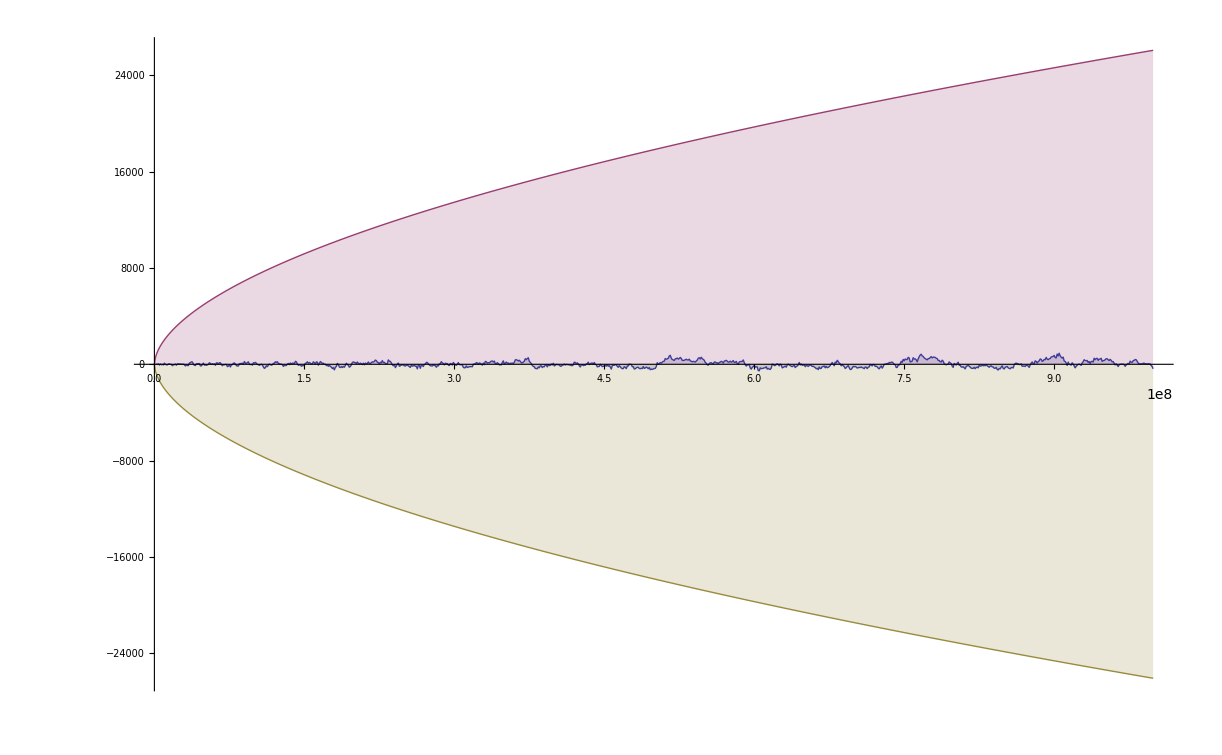

```mathematica
p[n_] := Sum[ 1/j PrimePi[ n^(1/j)],{j,1, Log[2,n]}]
DiscretePlot[ {LogIntegral[n]-p[n],1/(8 Pi) n^(1/2) Log[n], -1/(8 Pi) n^(1/2) Log[n]}, {n,1,1000000000, 1000000}]
```

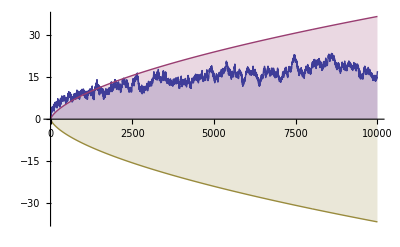

```mathematica
DiscretePlot[ {LogIntegral[n]-PrimePi[n],1/(8 Pi) n^(1/2) Log[n], -1/(8 Pi) n^(1/2) Log[n]}, {n,1,10000}]
```

```mathematica
pp[n_, j_, k_ ]:= pp[n,j,k] = If[ n<j, 0, 1/k - pp[Floor[n/j], 2, k+1 ] + pp[n,j+1,k]]
```

```mathematica
pp[100,2,1]
```

428/15

```mathematica
ps[n_, j_, k_ ]:=If[ n<j, 0, j(1/k - ps[Floor[n/j], 2, k+1 ]) + ps[n,j+1,k]]
```

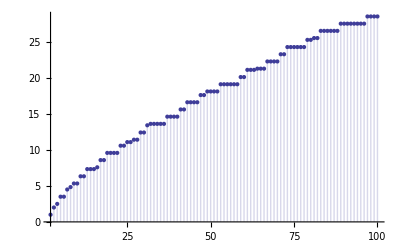

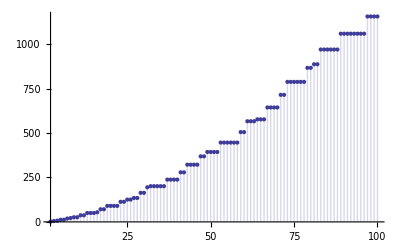

```mathematica
DiscretePlot[ pp[n,2,1], {n,2,100}]
DiscretePlot[ ps[n,2,1], {n,2,100}]
```

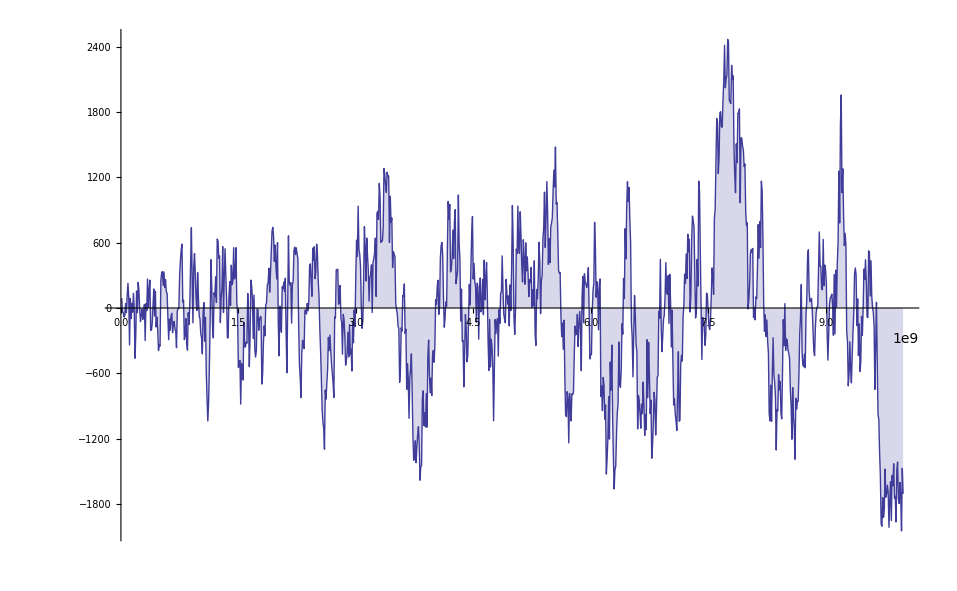

```mathematica
DiscretePlot[ {LogIntegral[n]-p[n]}, {n,1,10000000000, 10000000}]
```

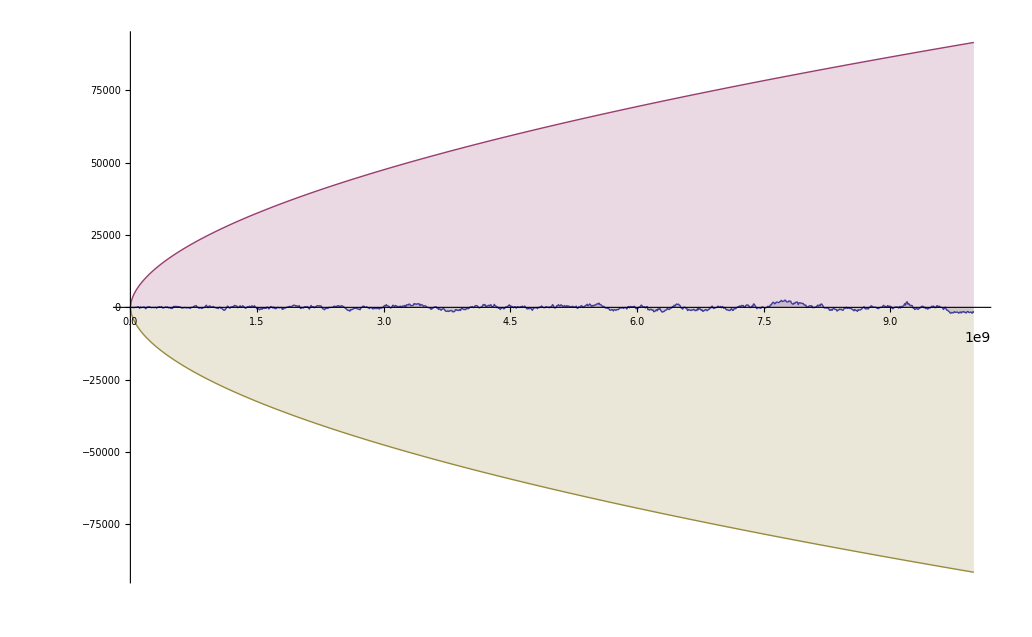

```mathematica
DiscretePlot[ {LogIntegral[n]-p[n],1/(8 Pi) n^(1/2) Log[n], -1/(8 Pi) n^(1/2) Log[n]}, {n,1,10000000000, 10000000}]
```

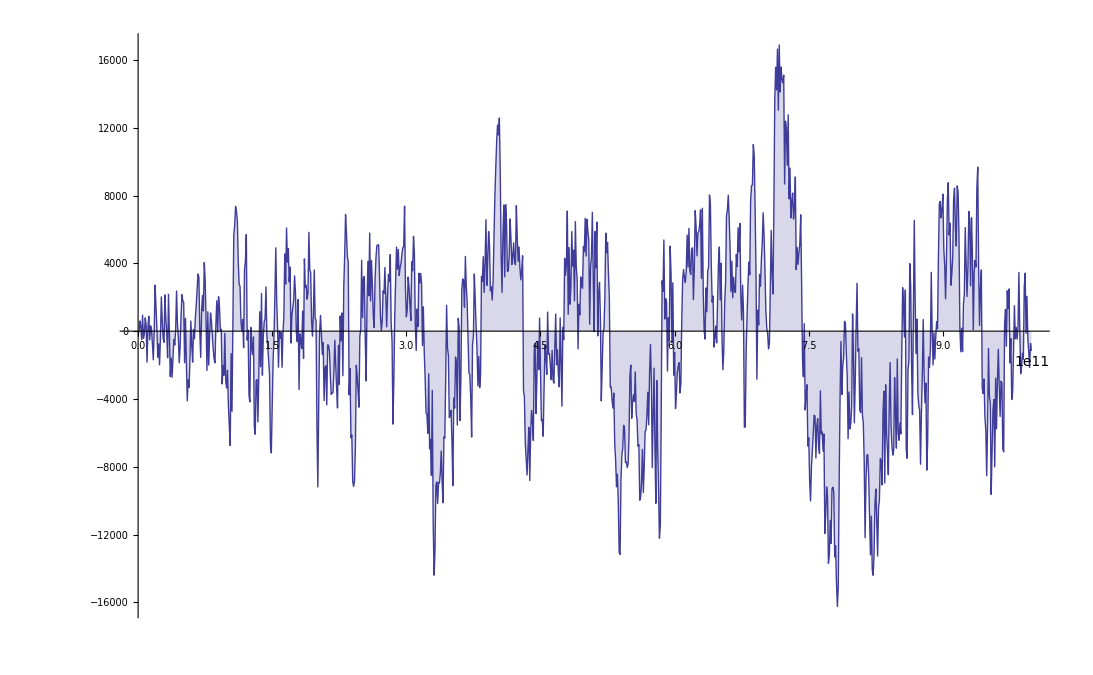

```mathematica
DiscretePlot[ {LogIntegral[n]-p[n]}, {n,1,1000000000000, 1000000000}]
```

```mathematica
LogIntegral[17.] - Log[Log[17]] - EulerGamma
```

7.25784

```mathematica
PrimeK[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
Linnik[n_,k_]:=1/k-Sum[If[j==1||n==j,0,Linnik[j,k+1]],{j,Divisors[n]}]
Table[{n,PrimeK[n],Linnik[n,1]},{n,2,100}]//TableForm
```

2 | 1 | 1
3 | 1 | 1
4 | 1/2 | 1/2
5 | 1 | 1
6 | 0 | 0
7 | 1 | 1
8 | 1/3 | 1/3
9 | 1/2 | 1/2
10 | 0 | 0
11 | 1 | 1
12 | 0 | 0
13 | 1 | 1
14 | 0 | 0
15 | 0 | 0
16 | 1/4 | 1/4
17 | 1 | 1
18 | 0 | 0
19 | 1 | 1
20 | 0 | 0
21 | 0 | 0
22 | 0 | 0
23 | 1 | 1
24 | 0 | 0
25 | 1/2 | 1/2
26 | 0 | 0
27 | 1/3 | 1/3
28 | 0 | 0
29 | 1 | 1
30 | 0 | 0
31 | 1 | 1
32 | 1/5 | 1/5
33 | 0 | 0
34 | 0 | 0
35 | 0 | 0
36 | 0 | 0
37 | 1 | 1
38 | 0 | 0
39 | 0 | 0
40 | 0 | 0
41 | 1 | 1
42 | 0 | 0
43 | 1 | 1
44 | 0 | 0
45 | 0 | 0
46 | 0 | 0
47 | 1 | 1
48 | 0 | 0
49 | 1/2 | 1/2
50 | 0 | 0
51 | 0 | 0
52 | 0 | 0
53 | 1 | 1
54 | 0 | 0
55 | 0 | 0
56 | 0 | 0
57 | 0 | 0
58 | 0 | 0
59 | 1 | 1
60 | 0 | 0
61 | 1 | 1
62 | 0 | 0
63 | 0 | 0
64 | 1/6 | 1/6
65 | 0 | 0
66 | 0 | 0
67 | 1 | 1
68 | 0 | 0
69 | 0 | 0
70 | 0 | 0
71 | 1 | 1
72 | 0 | 0
73 | 1 | 1
74 | 0 | 0
75 | 0 | 0
76 | 0 | 0
77 | 0 | 0
78 | 0 | 0
79 | 1 | 1
80 | 0 | 0
81 | 1/4 | 1/4
82 | 0 | 0
83 | 1 | 1
84 | 0 | 0
85 | 0 | 0
86 | 0 | 0
87 | 0 | 0
88 | 0 | 0
89 | 1 | 1
90 | 0 | 0
91 | 0 | 0
92 | 0 | 0
93 | 0 | 0
94 | 0 | 0
95 | 0 | 0
96 | 0 | 0
97 | 1 | 1
98 | 0 | 0
99 | 0 | 0
100 | 0 | 0

```mathematica
PrimeK[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
d[n_,z_]:=Product[Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Table[{n,D[d[n,z],z]/.z->0,PrimeK[n]},{n,2,100}]//TableForm
```

2 | 1 | 1
3 | 1 | 1
4 | 1/2 | 1/2
5 | 1 | 1
6 | 0 | 0
7 | 1 | 1
8 | 1/3 | 1/3
9 | 1/2 | 1/2
10 | 0 | 0
11 | 1 | 1
12 | 0 | 0
13 | 1 | 1
14 | 0 | 0
15 | 0 | 0
16 | 1/4 | 1/4
17 | 1 | 1
18 | 0 | 0
19 | 1 | 1
20 | 0 | 0
21 | 0 | 0
22 | 0 | 0
23 | 1 | 1
24 | 0 | 0
25 | 1/2 | 1/2
26 | 0 | 0
27 | 1/3 | 1/3
28 | 0 | 0
29 | 1 | 1
30 | 0 | 0
31 | 1 | 1
32 | 1/5 | 1/5
33 | 0 | 0
34 | 0 | 0
35 | 0 | 0
36 | 0 | 0
37 | 1 | 1
38 | 0 | 0
39 | 0 | 0
40 | 0 | 0
41 | 1 | 1
42 | 0 | 0
43 | 1 | 1
44 | 0 | 0
45 | 0 | 0
46 | 0 | 0
47 | 1 | 1
48 | 0 | 0
49 | 1/2 | 1/2
50 | 0 | 0
51 | 0 | 0
52 | 0 | 0
53 | 1 | 1
54 | 0 | 0
55 | 0 | 0
56 | 0 | 0
57 | 0 | 0
58 | 0 | 0
59 | 1 | 1
60 | 0 | 0
61 | 1 | 1
62 | 0 | 0
63 | 0 | 0
64 | 1/6 | 1/6
65 | 0 | 0
66 | 0 | 0
67 | 1 | 1
68 | 0 | 0
69 | 0 | 0
70 | 0 | 0
71 | 1 | 1
72 | 0 | 0
73 | 1 | 1
74 | 0 | 0
75 | 0 | 0
76 | 0 | 0
77 | 0 | 0
78 | 0 | 0
79 | 1 | 1
80 | 0 | 0
81 | 1/4 | 1/4
82 | 0 | 0
83 | 1 | 1
84 | 0 | 0
85 | 0 | 0
86 | 0 | 0
87 | 0 | 0
88 | 0 | 0
89 | 1 | 1
90 | 0 | 0
91 | 0 | 0
92 | 0 | 0
93 | 0 | 0
94 | 0 | 0
95 | 0 | 0
96 | 0 | 0
97 | 1 | 1
98 | 0 | 0
99 | 0 | 0
100 | 0 | 0